```mathematica
massfn[mmax_,m0_,a_,t_]:=((1-(1-(m0/mmax)^(1/4))*E^(-a*t/(4*mmax^(1/4)))))^4*mmax
```

```mathematica
massdecay[mmax_,a_,t_]:=mmax*E^(-a*((-1*t)+8000))
```

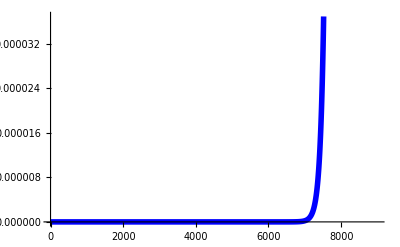

```mathematica
Plot[massdecay[100,.01,x],{x,0,9000},PlotStyle->{Thickness[.01],Blue}]
```

```mathematica
mmin=30
```

30

```mathematica
mintime=x/.NMinimize[Abs[massfn[100,1,.01,x]-massdecay[100,.0002,3000]],x][[2]]
```

1427.53

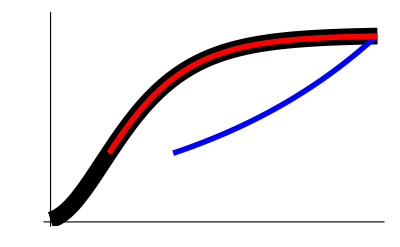

```mathematica
pltout=Show[{Plot[massfn[100,1,.01,x],{x,0,8000},PlotStyle->{Thickness[.03],Black},Ticks->False,AxesStyle->Thickness[.005]],Plot[massdecay[100,.0002,x],{x,3000,7950},PlotStyle->{Thickness[.01],Blue}],Plot[massfn[100,1,.01,x],{x,mintime,8000},PlotStyle->{Thickness[.01],Red},Ticks->False]},PlotRange->{All,{0,110}}]
```